## Word Ladders

Consider the graph of all 5 letter English words with an edge between two words if they differ by exactly one letter.

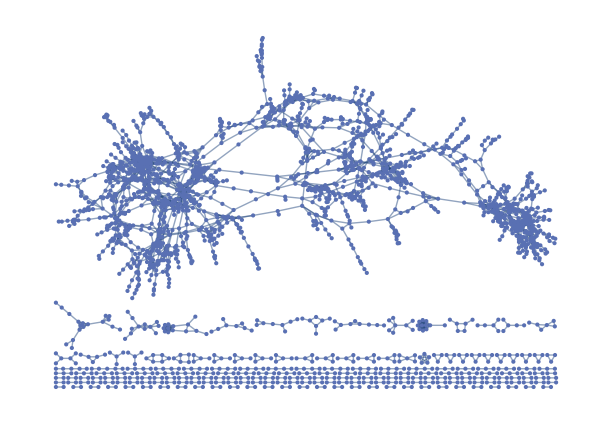

```mathematica
WordGraph=Graph[UndirectedEdge@@@Cases[Subsets[Cases[WordList[],w_/;StringLength@w==5],{2}],{a_,b_}/;HammingDistance[a,b]==1]]
```

A “word ladder” is a sequence of words such that consecutive words differ by exactly one letter.  This is a path in the word graph.

```mathematica
WordLadder[w1_,w2_]:=FindShortestPath[WordGraph,w1,w2];
WordLadder["black","white"]
```

{black,clack,click,crick,trick,trice,trite,write,white}

## Football scheduling

Consider the graph with each vertex the 32 NFL football teams and an edge between teams if they play a game during the 2025 season (there can be multiple edges between two teams and each team plays itself during the bye week).  We would like to color the edges with 18 colors such that no vertex uses one color twice (each color represents a week in the 18 week season) to find a NFL schedule.

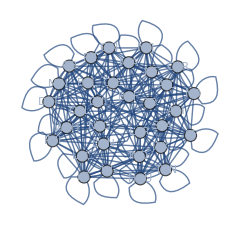
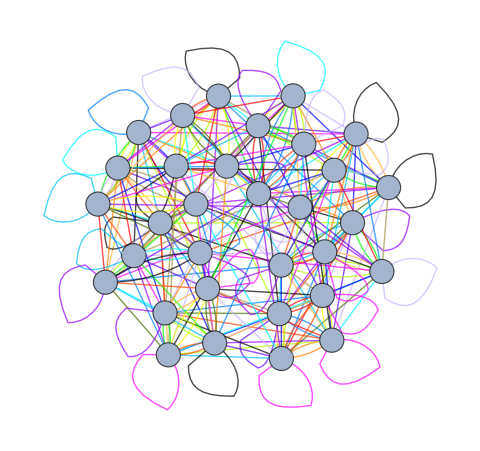

```mathematica
colors={RGBColor[1., 0., 0.],RGBColor[1., 0.27, 0.],RGBColor[1., 0.5, 0.],RGBColor[1., 0.7, 0.2],RGBColor[1., 1., 0.],RGBColor[0.7, 1., 0.],RGBColor[0.27, 0.45, 0.],RGBColor[0., 1., 0.],RGBColor[0.64, 0.58, 0.29],RGBColor[0., 1., 1.],RGBColor[0., 0.75, 1.],RGBColor[0., 0.5, 1.],RGBColor[0., 0., 1.],RGBColor[0.4, 0., 1.],RGBColor[0.6, 0., 1.],RGBColor[0.8, 0.7000000000000001, 1],RGBColor[1., 0., 1.],RGBColor[0., 0., 0.]};season=UndirectedEdge@@@ToExpression@Import["/home/tony/Courses/Math335/Fall2025/2025NFLseason.txt"];
{NFL=Graph[season,VertexLabels->Placed[Automatic,Center],VertexSize->.66,ImageSize->Medium],
Annotate[NFL,{EdgeStyle->Thread[EdgeList[NFL]->FindEdgeColoring[NFL,colors]]}]}
```

## Sudoku

Let vertices be the positions in a 9x9 grid and draw an edge between two positions if they are in the same row, column, or 3x3 block as in a Sudoku puzzle.

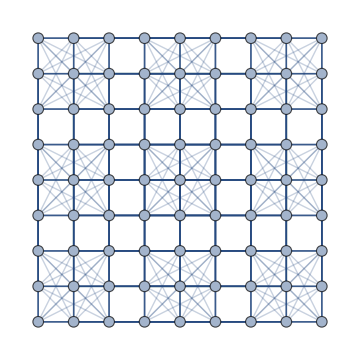

```mathematica
G2=Graph[UndirectedEdge@@@Cases[Subsets[Tuples[Range@9,2],{2}],{{a_,b_},{c_,d_}}/;a==c||b==d||{Ceiling[a/3],Ceiling[b/3]}=={Ceiling[c/3],Ceiling[d/3]}]];
Graph[G2,VertexCoordinates->VertexList@G2,ImageSize->Medium,VertexSize->0.3,EdgeStyle->Directive[Opacity[.25]]]
```

The edges are drawn with straight lines, so some of the edges are drawn on top of one another. 

To solve the Sodoku puzzle, we are looking to color the vertices with 9 colors such that adjacent vertices get different colors.

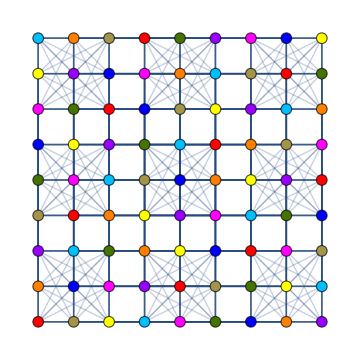

```mathematica
FindVertexColoring[G2,colors[[;;;;2]]];
Graph[G2,VertexCoordinates->VertexList@G2,VertexSize->0.3,EdgeStyle->Directive[Opacity[.25]],{VertexStyle->Thread[VertexList[G2]->%]},ImageSize->Medium]
```

## Printed Circuit Boards

Consider the graph with each vertex a hole in a printed circuit board (one example is below).  Draw an edge between every pair of holes, and weight the edge with the distance a robotic drill must move when traveling from one hole to another.

```mathematica
Show[Import["/home/tony/Courses/Math335/Fall2025/PCB-Layout-3262583308.jpg"],ImageSize->Medium]
```

-Graphics-

We would like to find the path of shortest weight to instruct the robotic arm how to move most efficiently when drilling the holes. The example below shows one pattern of holes (not the same as the circuit board in the image, the corresponding graph, and the solution for the path of the robotic arm of least cost.

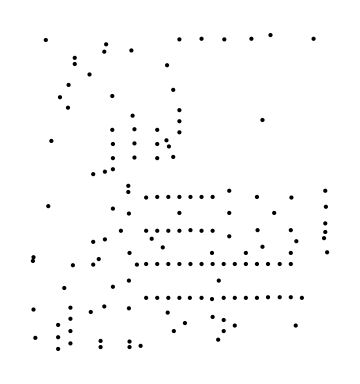
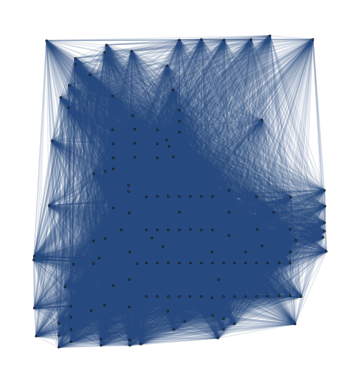
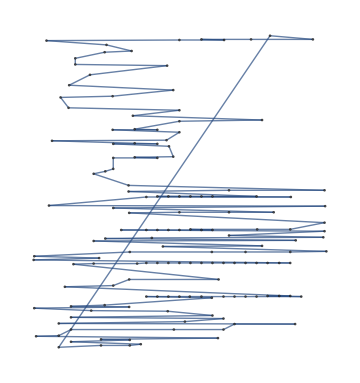

```mathematica
Holes=Reverse/@Sort[ToExpression@Import["/home/tony/Courses/Math335/Fall2025/Holes.txt"]][[-150;;]];
G1=Graph[UndirectedEdge@@@Subsets[Holes,{2}],EdgeWeight->ManhattanDistance@@@Subsets[Holes,{2}]];
{Graphics[Point/@Holes,ImageSize->Medium],
Graph[G1,VertexCoordinates->Holes,VertexSize->Large,EdgeStyle->Directive[Opacity[.1]],ImageSize->Medium],
Graph[PathGraph@Last@FindShortestTour@G1,VertexCoordinates->Holes,VertexSize->Large,ImageSize->Medium]}
```